# RandomWeightedGraph

Create a random weighted graph

## Definition

```mathematica
RandomWeightedGraph[{vertices_,edges_},randomFunction_,options:OptionsPattern[]]:=Block[{randomGraph} ,randomGraph=RandomGraph[{vertices,edges},options];Graph[randomGraph,EdgeWeight->(Map[#->randomFunction[]&,EdgeList[randomGraph]])]];

RandomWeightedGraph[{vertices_,edges_},randomFunction_,k_?IntegerQ,options:OptionsPattern[]]:=Table[RandomWeightedGraph[{vertices,edges},randomFunction,options],k]

RandomWeightedGraph[{vertices_,edges_},randomFunction_,array_List,options:OptionsPattern[]]:=Array[RandomWeightedGraph[{vertices,edges},randomFunction,options]&,array]

RandomWeightedGraph[graphDistribution_,randomFunction_,options:OptionsPattern[]]:=Block[{randomGraph} ,randomGraph=RandomGraph[graphDistribution,options];Graph[randomGraph,EdgeWeight->(Map[#->randomFunction[]&,EdgeList[randomGraph]])]];

RandomWeightedGraph[graphDistribution_,randomFunction_,k_?IntegerQ,options:OptionsPattern[]]/;k>=1:=Table[RandomWeightedGraph[graphDistribution,randomFunction,options],k]

RandomWeightedGraph[graphDistribution_,randomFunction_,array_List,options:OptionsPattern[]]:=Array[RandomWeightedGraph[graphDistribution,randomFunction,options]&,array]
RandomWeightedGraph::usage="RandomWeightedGraph[{vertices, edges},  randomFunction] creates a random graph with vertices vertices and edges edges with edge weights given by randomFunction\nRandomWeightedGraph[{vertices, edges}, , randomFunction, k] creates k random graphs with vertices vertices and edges edges with edge weights given by randomFunction\nRandomWeightedGraph[{vertices, edges}, , randomFunction, array] creates a dimensions array of random graphs with vertices vertices and edges edges with edge weights given by randomFunction\nRandomWeightedGraph[distribution, , randomFunction] creates a random graph with graph distribution distribution with edge weights given by randomFunction\nRandomWeightedGraph[distribution, , randomFunction, k] creates k random graphs with graph distribution distribution with edge weights given by randomFunction\nRandomWeightedGraph[distribution, , randomFunction, array] creates a dimensions array of random graphs with graph distribution distribution with edge weights given by randomFunction";
```

## Documentation

### Usage

RandomWeightedGraph[{vertices,edges},randomfunction]

generate a random graph with vertices vertices and edges edges with edge weights given by randomfunction.

RandomWeightedGraph[{vertices,edges},randomfunction,k]

generate k random graphs with vertices vertices and edges edges with edge weights given by randomfunction.

RandomWeightedGraph[{vertices,edges},randomfunction,dimensions]

generate a dimensions array filled with random graphs with vertices vertices and edges edges with edge weights given by randomfunction.

RandomWeightedGraph[graphdistribution,randomfunction]

generate a random graph with graphdistribution with edge weights given by randomfunction.

RandomWeightedGraph[graphdistribution,randomfunction,k]

generate k random graphs with graphdistribution with edge weights given by randomfunction.

RandomWeightedGraph[graphdistribution,randomfunction,dimensions]

generate a dimensions array filled with random graphs with graphdistribution with edge weights given by randomfunction.

### Details & Options

randomfunction should be RandomReal or RandomInteger

randomfunction should end in &. For example RandomReal[{1,7}]& or RandomInteger[{1,7}]&.

randomfunction should either be called with no arguments like RandomReal[]&, a max argument like RandomReal[7]&, or a range {x_min,x_max} like RandomReal[{1,7}]&. RandomReal[range,n] and RandomReal[range,{n_1,n_2,…}] should not be used for example.

The function accepts the same options as graph.

## Examples

### Basic Examples

Make a random graph:

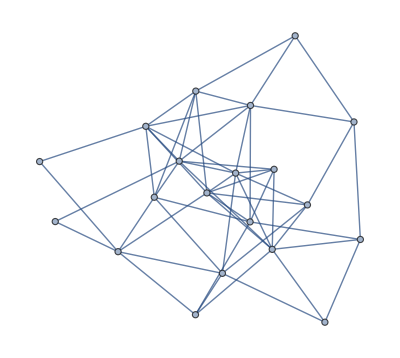

```mathematica
RandomWeightedGraph[{20,54},RandomReal[]&]
```

Make a random graph with edge weights between 1 and 7:

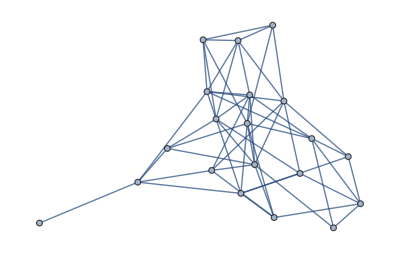

```mathematica
RandomWeightedGraph[{20,54},RandomReal[{1,7}]&]
```

Make a random graph with integer weights:

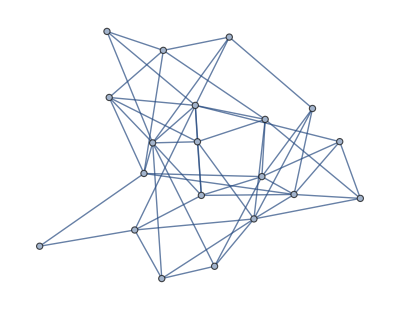

```mathematica
RandomWeightedGraph[{20,54},RandomInteger[{1,7}]&]
```

Make a list of random graphs:

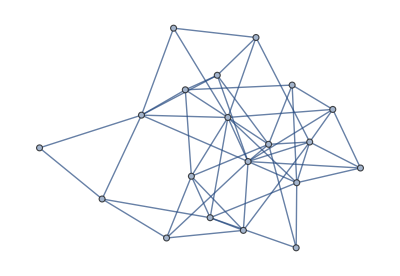
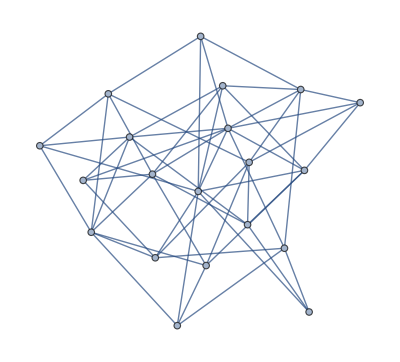
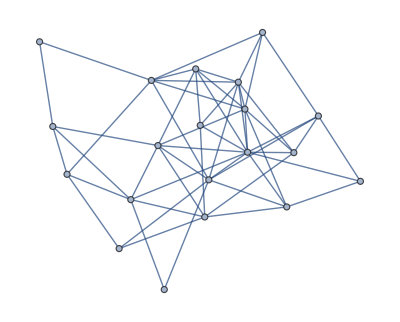
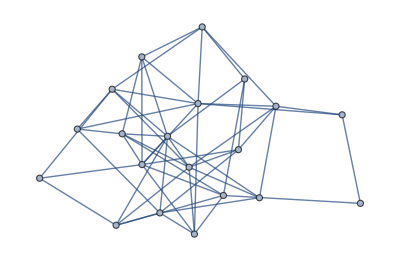
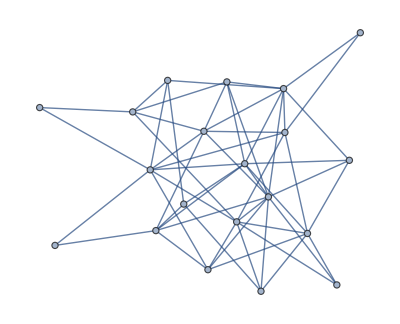
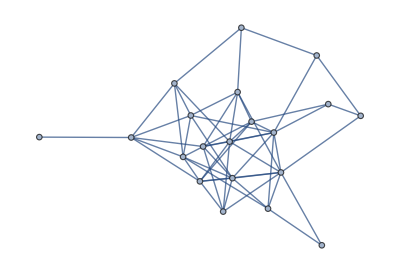
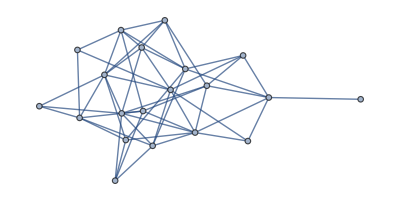

```mathematica
RandomWeightedGraph[{20,54},RandomInteger[{1,7}]&,7]
```

Make an array of random graphs:

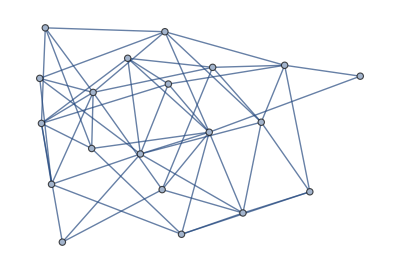
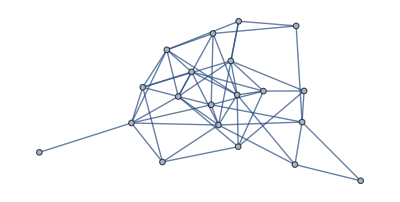
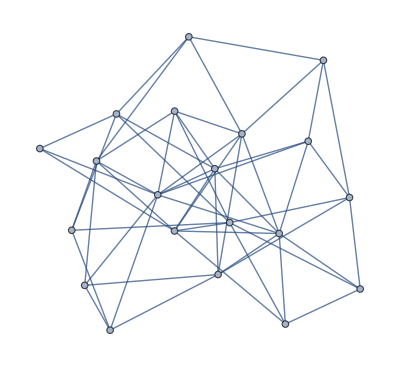
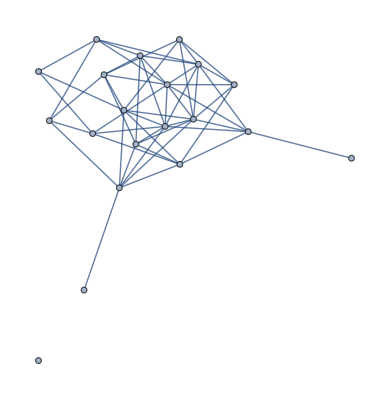
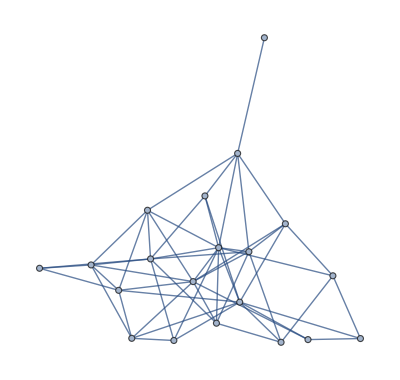
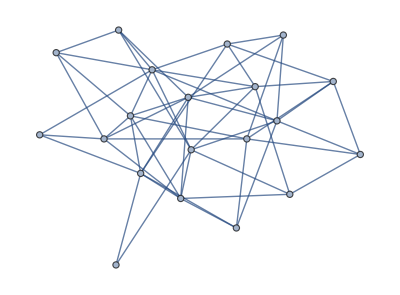
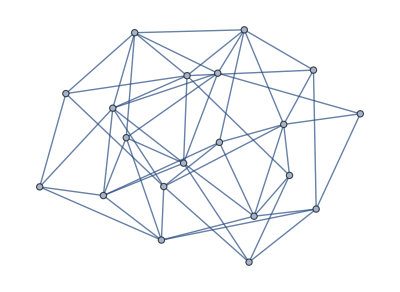
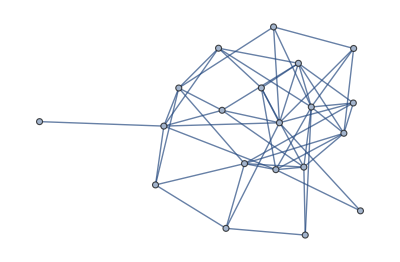

```mathematica
RandomWeightedGraph[{20,54},RandomInteger[{1,7}]&,{2,3,5},]
```

Make a random graph with a graph distribution:

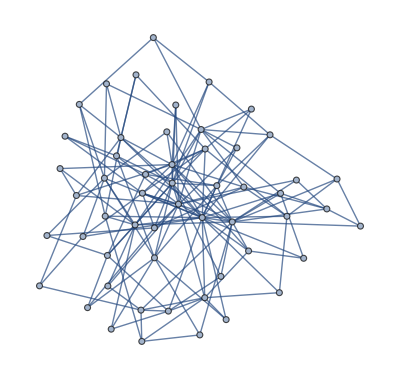

```mathematica
RandomWeightedGraph[BarabasiAlbertGraphDistribution[54,3],RandomInteger[{1,7}]&]
```

Make a list of graphs with a graph distribution:

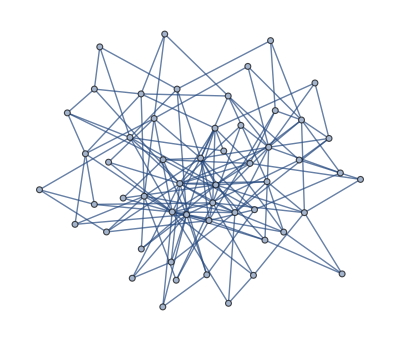
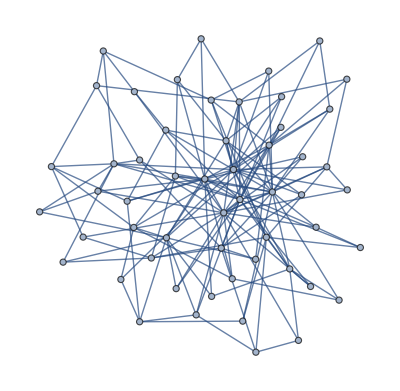
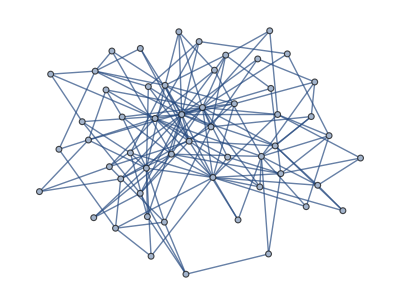
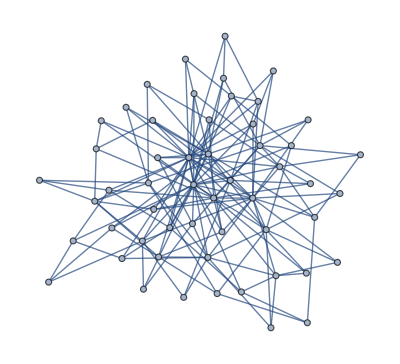
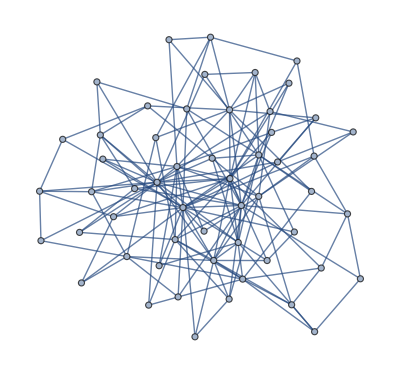
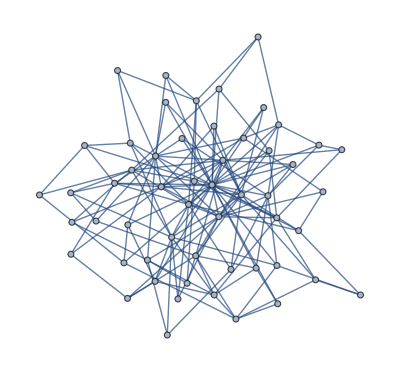
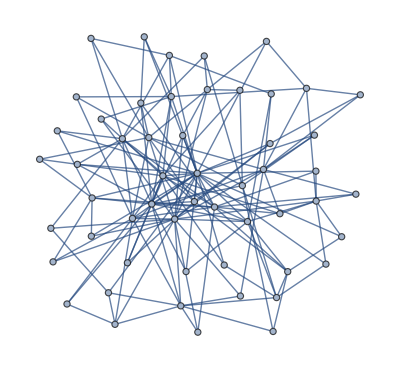

```mathematica
RandomWeightedGraph[BarabasiAlbertGraphDistribution[54,3],RandomInteger[{1,7}]&,7]
```

Make an array of graphs with a graph distribution:

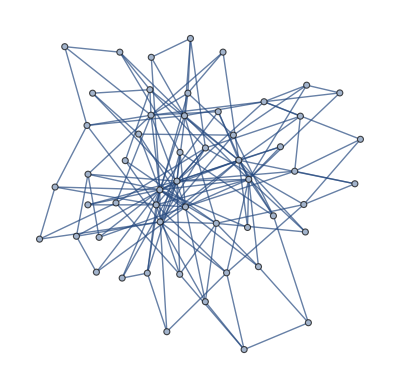
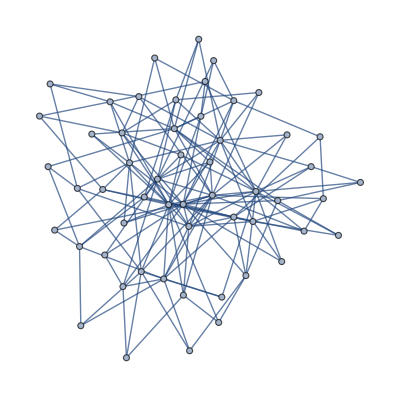
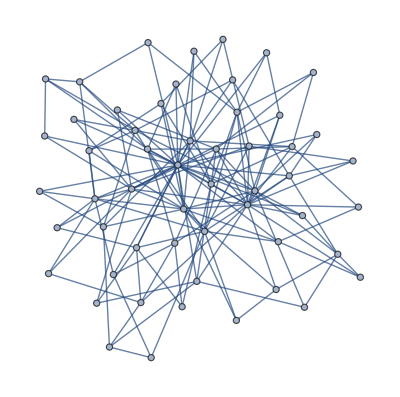
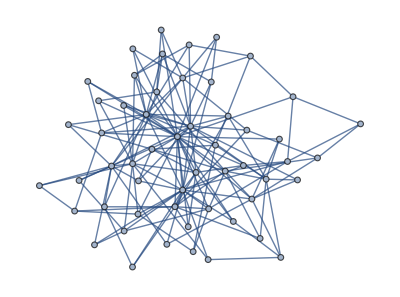
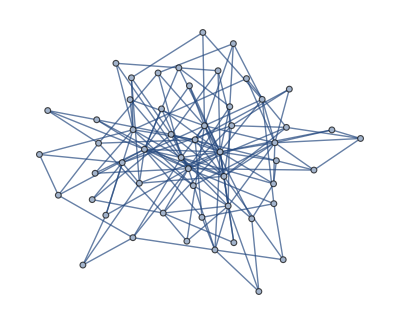
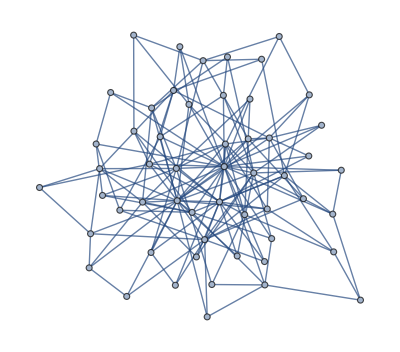
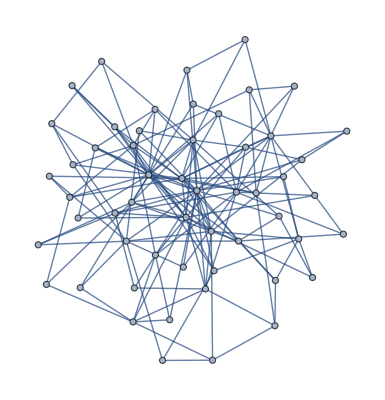
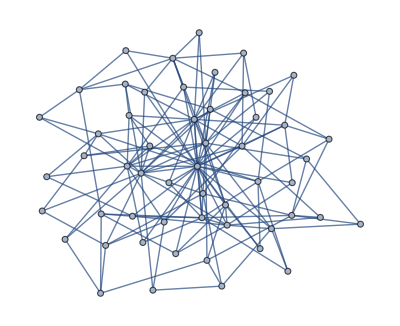

```mathematica
RandomWeightedGraph[BarabasiAlbertGraphDistribution[54,3],RandomInteger[{1,7}]&,{2,3,5},]
```

Make a graph with a spatial graph distribution:

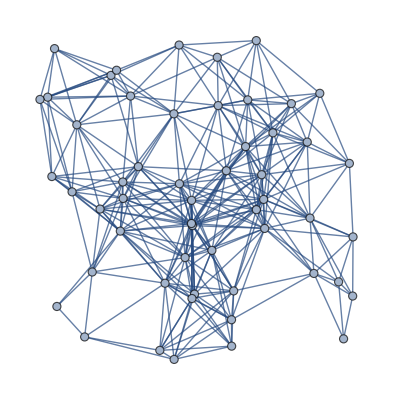

```mathematica
RandomWeightedGraph[SpatialGraphDistribution[54,0.3],RandomInteger[{1,7}]&]
```

### Scope

### Options

#### EdgeLabels

Create a random weighted graph with integer weights with edge labels:

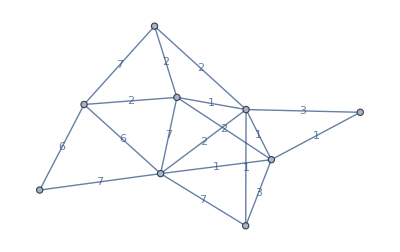

```mathematica
RandomWeightedGraph[{9,18},RandomInteger[{1,7}]&,EdgeLabels->"EdgeWeight"]
```

### Applications

### Properties and Relations

Find a solution to the undirected Chinese Postman problem for a random weighted graph:

```mathematica
FindPostmanTour[RandomWeightedGraph[{20,54},RandomReal[]&]]
```

{{1<->2,2<->20,20<->19,19<->16,16<->14,14<->20,20<->18,18<->12,12<->20,20<->17,17<->15,15<->12,12<->6,6<->12,12<->13,13<->14,14<->19,19<->9,9<->18,18<->7,7<->17,17<->4,4<->18,18<->11,11<->14,14<->7,7<->10,10<->9,9<->7,7<->19,19<->3,3<->16,16<->5,5<->9,9<->5,5<->13,13<->11,11<->15,15<->4,4<->9,9<->11,11<->8,8<->5,5<->7,7<->14,14<->2,2<->7,7<->11,11<->3,3<->9,9<->3,3<->5,5<->4,4<->6,6<->2,2<->4,4<->3,3<->2,2<->1}}

Make a table highlighting the steps by constructing directed graphs:

```mathematica
First[FindPostmanTour[RandomWeightedGraph[{20,54},RandomReal[]&]]]/.{x_<->y_->x->y}
```

{1->20,20->16,16->12,12->15,15->14,14->19,19->14,14->2,2->14,14->6,6->20,20->7,7->18,18->9,9->17,17->9,9->18,18->5,5->15,15->7,7->17,17->11,11->13,13->11,11->6,6->16,16->9,9->13,13->4,4->11,11->9,9->6,6->17,17->8,8->10,10->12,12->5,5->16,16->3,3->8,8->4,4->11,11->2,2->10,10->2,2->13,13->7,7->3,3->16,16->1,1->11,11->5,5->6,6->2,2->5,5->1,1->6,6->3,3->2,2->7,7->4,4->1}

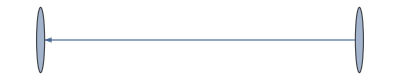
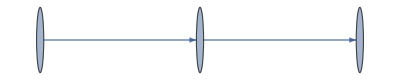
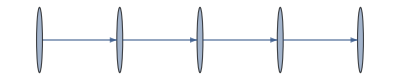
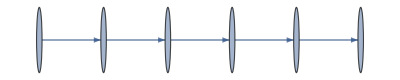
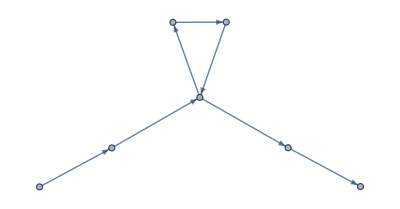
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graph@Take[First[FindPostmanTour[RandomWeightedGraph[{20,54},RandomReal[]&]]]/.{x_<->y_->x->y},k],{k,Length[First[FindPostmanTour[RandomWeightedGraph[{20,54},RandomReal[]&]]]/.{x_<->y_->x->y}]}]
```

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Peter Burbery

### Keywords

Graphs

Chinese Postman Problem

Arc Routing

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

RandomGraph

BarabasiAlbertGraphDistribution

BernoulliGraphDistribution

### Related Resource Objects

EulerizeGraph

UndirectedGraphToMixedGraph

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.